```mathematica
NALOGA 1
```

```mathematica
ClearAll[daljica, Dolzina, EnacbaNosilke]
```

```mathematica
Daljica[{AA_, BB_}]:= {{x,y}, {x1, y1}}
```

```mathematica
daljica=Daljica[{-1, 1}, {3,-1}]
daljica2=Daljica[{-1,-1}, {3,1}]
daljica3=Daljica[{-1,2},{3,0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]]:=Norm[AA-BB]
Dolzina[daljica]
```

2 √5

```mathematica
ClearAll[x,y,EnacbaNosilke]
EnacbaNosilke[Daljica[AA_,BB_]]:= Module[{x1,y1,x2,y2,k,n},
{x1,y1}=AA;
 {x2,y2}=BB;
 k=(y2-y1)/(x2-x1);
 n=n/.First[Solve[y1==k*x1+n, n]];
y==k*x+n
]
```

```mathematica
Slika[Daljica[AA_,BB_]]:=Line[{AA,BB}]
Slika[daljica]
```

Line[{{-1,1},{3,-1}}]

```mathematica
EnacbaNosilke[daljica]
```

y==1/2-x/2

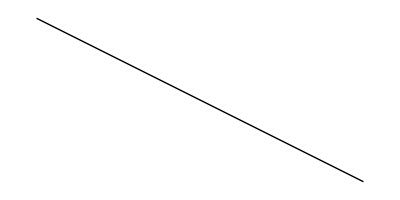

```mathematica
Graphics[Line[{{-1, 1}, {3,-1}}]]
```

```mathematica
NALOGA 2
```

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:=  Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]]
Presek[daljica, daljica2]
```

{1,0}

```mathematica
NALOGA 3
```

```mathematica
m1=Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}, {0,0}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
z= Slika[Mnogokotnik[t__]]:=Line[t]
Slika[m1]
```

Line[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Narisi[m__Mnogokotnik]:=Graphics[Point[AA],Point[BB],Point[CC],Point[DD], Line[{AA,BB},{BB,CC},{CC,DD},{DD,AA}]]
Narisi[m1]
```

-Graphics-

```mathematica
PravilniNKotnik[n_,r_]:=
```

```mathematica
PravilniNKotnik[n_,r_,phi_]:=
```

```mathematica
Daljice[Mnogokotnik[t__]]:=Partition[{t},2,1]
Daljice[m1]
```

{{{0,0},{1,1}},{{1,1},{0,3}},{{0,3},{-1,2}},{{-1,2},{0,0}}}

```mathematica
Partition[{1,2,3,4,5},2]
```

{{1,2},{3,4}}

```mathematica
Partition[{1,2,3,4,5},2,1]
```

{{1,2},{2,3},{3,4},{4,5}}

```mathematica
NALOGA 4
```

```mathematica
Presek[m_Mnogokotnik,d_Daljica]:=DeleteDuplicates[Mnogokotnik, Daljica]
Presek[m1, daljica]
```

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[Mnogokotnik,Daljica].

DeleteDuplicates[Mnogokotnik,Daljica]

```mathematica
NALOGA 5
```

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[f,{1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
Outer[f,{1,2,3},{4,5,6}]
```

{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}}

```mathematica
Outer - vsakega z vsakim naredi pare
Flatten - pred vsak par postavi f, naredi funkcijo
```

```mathematica
Flatten[{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}},1]
```

{f[1,4],f[1,5],f[1,6],f[2,4],f[2,5],f[2,6],f[3,4],f[3,5],f[3,6]}

```mathematica
NALOGA 6
```

```mathematica
ClearAll[A,B]
```

```mathematica
Izračunaj vektorski produkt v1 in v2, če imaš podane 3 točke.
```

```mathematica
A:= {-3,-2,0}
B:= {3,-3,1}
Ž:={5,0,2}
v1[A_,B_]:=B-A
v2[A_,Ž_]:=Ž-A
v1[A,B]
v2[A,Ž]
```

{6,-1,1}

{8,2,2}

```mathematica
v1:={6,-1,1}
v2:={8,2,2}
```

```mathematica
Cross[v1,v2]
```

{-4,-4,20}